First, the various stellar parameters for our two-point model. 
Let’s just start with the first segment, so x_0=0, Δx=h.

```mathematica
x0=0;
Δx=h; (* Δx=Subscript[x, 1]-Subscript[x, 0] *)
t[x_]:= (x-x0) / Δx ;
```

The Cubic Hermit Basis functions

```mathematica
H30[x_]:=1−3*t[x]^2+2*t[x]^3;
H31[x_]:=t[x]−2*t[x]^2+t[x]^3;
H32[x_]:=−t[x]^2+t[x]^3;
H33[x_]:=3*t[x]^2−2*t[x]^3;
```

```mathematica
P[x_]:=Subscript[α, 0] H30[x]+Subscript[α, 1] h H31[x]+Subscript[α, 2] h H32[x]+Subscript[α, 3] H33[x]
```

At the first segment, α_1=0.

```mathematica
Subscript[α, 1]=0;
```

```mathematica
Collect[P[x],x]
```

α_0+x^3 ((2 α_0)/h^3+α_2/h^2-(2 α_3)/h^3)+x^2 (-(3 α_0)/h^2-α_2/h+(3 α_3)/h^2)

```mathematica
Collect[ D[P[x], x], x]
```

x^2 ((6 α_0)/h^3+(3 α_2)/h^2-(6 α_3)/h^3)+x (-(6 α_0)/h^2-(2 α_2)/h+(6 α_3)/h^2)

From the stellar structure equations, we see that we can find m^2= (-8π)/a∫_0^x x^4*P'*dx .
However, we just saw that P’ is proportional to x•w, where w is a linear polynomial. 
Then   m^2= x^6*w  , and we choose to write w in linear Hermite form.

```mathematica
H10[x_]:=1-t[x];
H11[x_]:=t[x];
w[x_] := Subscript[β, 0] H10[x]+Subscript[β, 1] H11[x];
```

We can find β_i in terms of α_i.

```mathematica
LHS[x_]:=(-8*Pi/a)*Integrate[x^4 D[P[x], x],{x,0,x}];
Collect[ LHS[x],x]
```

-(8 π x^7 ((6 α_0)/(7 h^3)+(3 α_2)/(7 h^2)-(6 α_3)/(7 h^3)))/a-(8 π x^6 (-α_0/h^2-α_2/(3 h)+α_3/h^2))/a

```mathematica
RHS[x_]:=x^6 w[x];
Collect[RHS[x],x]
```

x^6 β_0+x^7 (-β_0/h+β_1/h)

```mathematica
Solve[{
-(8 π x^6 (-Subscript[α, 0]/h^2-Subscript[α, 2]/(3 h)+Subscript[α, 3]/h^2))/a==x^6 Subscript[β, 0],
-(8 π x^7 ((6 Subscript[α, 0])/(7 h^3)+(3 Subscript[α, 2])/(7 h^2)-(6 Subscript[α, 3])/(7 h^3)))/a==x^7 (-Subscript[β, 0]/h+Subscript[β, 1]/h)},{Subscript[β, 0],Subscript[β, 1]}]
```

{{β_0→(8 (3 π α_0+h π α_2-3 π α_3))/(3 a h^2),β_1→-(8 (-3 π α_0+2 h π α_2+3 π α_3))/(21 a h^2)}}

```mathematica
Subscript[β, 0]=(8 (3 π Subscript[α, 0]+h π Subscript[α, 2]-3 π Subscript[α, 3]))/(3 a h^2);
Subscript[β, 1]=-(8 (-3 π Subscript[α, 0]+2 h π Subscript[α, 2]+3 π Subscript[α, 3]))/(21 a h^2);
```

```mathematica
FullSimplify[w[x]]
```

(8 π (3 (7 h-6 x) α_0+h (7 h-9 x) α_2+3 (-7 h+6 x) α_3))/(21 a h^3)

```mathematica
m[x_]:=x^3 w[x]^(1/2)
```

```mathematica
P[x]
```

(1-(3 x^2)/h^2+(2 x^3)/h^3) α_0+h (-x^2/h^2+x^3/h^3) α_2+((3 x^2)/h^2-(2 x^3)/h^3) α_3

Finally, from stellar structure we see that ρ =m'/(4π x^2)= 3/(4π)w^(1/2)[1+x/6 w'/w]

```mathematica
FullSimplify[-x^2/a*(D[P[x], x])/m[x]]
```

(√(21/(2 π)) (6 (h-x) α_0+h (2 h-3 x) α_2+6 (-h+x) α_3))/(2 a h^3 √((3 (7 h-6 x) α_0+h (7 h-9 x) α_2+3 (-7 h+6 x) α_3)/(a h^3)))

```mathematica
ρ[x_]:=(√(21/(2 π)) (6 (h-x) Subscript[α, 0]+h (2 h-3 x) Subscript[α, 2]+6 (-h+x) Subscript[α, 3]))/(2 a h^3 √((3 (7 h-6 x) Subscript[α, 0]+h (7 h-9 x) Subscript[α, 2]+3 (-7 h+6 x) Subscript[α, 3])/(a h^3)))
```

Now we can begin to find the coefficients. α_(0,1,5) are known from the boundary conditions.
α_4 comes from the gradient of P at the surface, so α_4= -aρ_s

```mathematica
Subscript[α, 0]=Subscript[P, c];
Subscript[α, 3]=Subscript[P, s];
Subscript[α, 2]=-a*Subscript[ρ, s];
```

We can find α_3in terms of α_2 from ρ_s, and find α_2from ρ_c=3/(4π)(w(0))^(1/2)[1+x/6(w'(0))/(w(0))].

Now let’s set some values and make some plots.

```mathematica
h=1;
a=2;
Subscript[P, c]=1;
Subscript[P, s]=0;
Subscript[ρ, c]=1;
Subscript[ρ, s]=1;
```

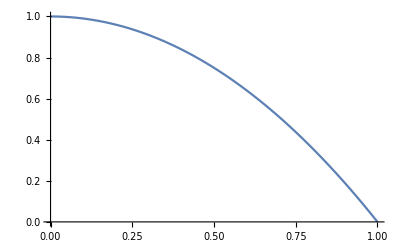

```mathematica
Plot[P[x],{x,0,h}]
```